Copyright (C) 2016 Leo Fang <leofang@phy.duke.edu>

This program is free software. It comes without any warranty, to the extent permitted by applicable law. You can redistribute it and/or modify it under the terms of the WTFPL, Version 2, as published by Sam Hocevar. See the accompanying LICENSE file or http://www.wtfpl.net/ for more details.

```mathematica
(* read input parameters *)
```

```mathematica
Import[NotebookDirectory[]<>"../k0a_0.5pi_on_new"]
```

{{nx=200},{Nx=10000},{Ny=20000},{Delta=0.0100000000},{k=1.5707963268},{w0=1.5707963268},{Gamma=0.0785398163}}

```mathematica
%//ToExpression (* ignore the Gamma thing -- it has name conflict with the Mathematica Gamma function *)
```

Set::wrsym: Symbol Gamma is Protected.

{{200},{10000},{20000},{0.01},{1.5708},{1.5708},{0.0785398}}

```mathematica
gamma=%[[-1]]//First
```

0.0785398

```mathematica
(* setup based on input parameters *)
```

```mathematica
Xmin=-(Nx+nx+1)Delta
```

-102.01

```mathematica
Xmax=(Nx)Delta
```

100.

```mathematica
qubit1=-nx/2*Delta
```

-1.

```mathematica
qubit2=nx/2*Delta
```

1.

```mathematica
(* read computed two-photon wavefunction *)
```

```mathematica
χ=ReadList[NotebookDirectory[]<>"../k0a_0.5pi_on_new.abs_chi.out",Number,RecordLists->True]; (* abs value *)
```

```mathematica
(* plot Subscript[g, 2](τ,t)=|χ(a+Δ,a+Δ+τ,t)|^2 as an animation in t; unit: Γ*t *)
```

```mathematica
Manipulate[ListPlot[χ[[i]]^2,Joined->True,PlotMarkers->None,DataRange->{0,(Nx-nx/2+1)Delta*gamma},PlotRange->{0,All},GridLines->{{(qubit2-qubit1)*gamma},None}],{i,1,Length[χ],1}]
```

```mathematica
(* plot Subscript[g, 2](τ,t)=|χ(a+Δ,a+Δ+τ,t)|^2 at the cut-off time t=(Ny-1)Δ; unit: Γ*t *)
```

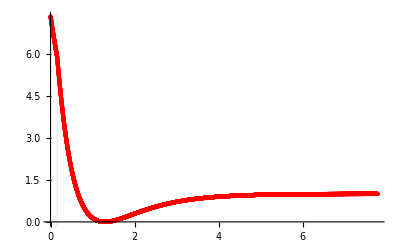

```mathematica
ListPlot[χ[[-1]]^2,Joined->False,PlotStyle->Red,DataRange->{0,(Nx-nx/2+1)Delta*gamma},PlotRange->{0,All},GridLines->{{(qubit2-qubit1)*gamma},None}]
```

```mathematica
Clear[χ](* the next file is memory consuming, so clear some memory first *)
```

```mathematica
(* read computed wavefunctions *)
```

```mathematica
bR=ReadList[NotebookDirectory[]<>"../k0a_0.5pi_on_new.re.out",Number,RecordLists->True]; (* real part*)
```

```mathematica
(* plot the real part of the first 10% (in time) solution *)
```

```mathematica
ny=0.1;
```

```mathematica
ListDensityPlot[bR[[1;;Ceiling[ny*Ny]]],DataRange->{{Xmin,Xmax},{0,(ny*Ny-1)*Delta}},PlotRange->{All,All},ColorFunction->"Warm",PlotLegends->Automatic,AspectRatio->Automatic,MaxPlotPoints->200]
```

-Graphics-

```mathematica
(* plot the real part of the entire solution *)
```

```mathematica
ListDensityPlot[bR[[1;;Ny]],DataRange->{{Xmin,Xmax},{0,(Ny-1)*Delta}},PlotRange->{All,All},ColorFunction->"Warm",PlotLegends->Automatic,AspectRatio->Automatic,MaxPlotPoints->{200,500}]
```

```mathematica
(* show the wave propagation as an animation *)
```

```mathematica
Manipulate[ListPlot[bR[[i]],Joined->True,PlotMarkers->None,DataRange->{Xmin,Xmax},PlotRange->{All,{-8,8}},GridLines->{{qubit1,qubit2},None}],{i,1,Length[bR],1}]
```